# Primordial Power Spectra of Cosmological Fluctuations with Generalized Uncertainty Principle and Maximum Length Quantum Mechanics (Numerical Analysis and Construction Figures File)

## Figure 3 a (Left Panel)

#### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* In order to use the Needs["ErrorBarLogPlots`"] command you need to install the "Error Bar Log Plots" package which can be installed directly from the zip file "ErrorBarLogPlots.zip" or you can download it from http://library.wolfram.com/infocenter/MathSource/6747/*)
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
```

### Full Dataset

```mathematica
data={{0.000086,0.94979,0.21666},{0.00010667,0.94649,0.213525},{0.00012473,0.94772,0.19478},{0.00014549,0.94841,0.17844},{0.00016969,0.9491,0.15394},{0.00019793,0.95116,0.14638},{0.00023085,0.95116,0.12852},{0.00026926,0.95116,0.114895},{0.00031406,0.95254,0.09991},{0.00036631,0.95391,0.093965},{0.00042725,0.95391,0.084105},{0.00049833,0.95391,0.07597},{0.00058124,0.95506,0.067225},{0.00067796,0.95666,0.063705},{0.00079074,0.95666,0.05845},{0.00092228,0.95689,0.05096},{0.0010757,0.95804,0.04626},{0.0012547,0.95804,0.044685},{0.0014634,0.95804,0.04126},{0.0017069,0.95804,0.039885},{0.0019655,0.95873,0.038535},{0.0023221,0.96079,0.038535},{0.0027084,0.96079,0.038535},{0.003159,0.96079,0.037285},{0.0036845,0.96079,0.03612},{0.0042974,0.96079,0.035645},{0.0050123,0.96079,0.035645},{0.0058461,0.96079,0.034475},{0.0068186,0.96079,0.03426},{0.0079529,0.96102,0.03396},{0.0092762,0.96216,0.03702},{0.010819,0.96216,0.037265},{0.012619,0.96125,0.03757},{0.014718,0.96056,0.03662},{0.017166,0.95941,0.037135},{0.020021,0.95941,0.038335},{0.023351,0.95804,0.03782},{0.027236,0.95781,0.03864},{0.031765,0.95621,0.03908},{0.037049,0.95529,0.040765},{0.043212,0.95529,0.04126},{0.0504,0.95529,0.04307},{0.058785,0.95529,0.04324},{0.068564,0.95529,0.0433},{0.079969,0.95529,0.047285},{0.093273,0.95529,0.047435},{0.10879,0.95529,0.05001},{0.12688,0.95483,0.052285},{0.14799,0.95391,0.05303},{0.17261,0.95391,0.054455},{0.20132,0.95391,0.054835},{0.23481,0.95391,0.057535},{0.27387,0.95391,0.05947},{0.31943,0.95368,0.064415},{0.37256,0.95231,0.065895},{0.43453,0.95116,0.068355},{0.50681,0.95116,0.07375},{0.59112,0.95093,0.07673},{0.68942,0.9491,0.07991},{0.8041,0.94841,0.092145},{0.93785,0.94772,0.09479},{1.0938,0.94589,0.100045},{1.2758,0.9452,0.11354},{1.3955,0.94429,0.120095},{1.7354,0.94108,0.13967},{2.024,0.94016,0.15637},{2.3606,0.93855,0.16645},{2.6156,0.9381,0.181885}}
```

{{0.000086,0.94979,0.21666},{0.00010667,0.94649,0.213525},{0.00012473,0.94772,0.19478},{0.00014549,0.94841,0.17844},{0.00016969,0.9491,0.15394},{0.00019793,0.95116,0.14638},{0.00023085,0.95116,0.12852},{0.00026926,0.95116,0.114895},{0.00031406,0.95254,0.09991},{0.00036631,0.95391,0.093965},{0.00042725,0.95391,0.084105},{0.00049833,0.95391,0.07597},{0.00058124,0.95506,0.067225},{0.00067796,0.95666,0.063705},{0.00079074,0.95666,0.05845},{0.00092228,0.95689,0.05096},{0.0010757,0.95804,0.04626},{0.0012547,0.95804,0.044685},{0.0014634,0.95804,0.04126},{0.0017069,0.95804,0.039885},{0.0019655,0.95873,0.038535},{0.0023221,0.96079,0.038535},{0.0027084,0.96079,0.038535},{0.003159,0.96079,0.037285},{0.0036845,0.96079,0.03612},{0.0042974,0.96079,0.035645},{0.0050123,0.96079,0.035645},{0.0058461,0.96079,0.034475},{0.0068186,0.96079,0.03426},{0.0079529,0.96102,0.03396},{0.0092762,0.96216,0.03702},{0.010819,0.96216,0.037265},{0.012619,0.96125,0.03757},{0.014718,0.96056,0.03662},{0.017166,0.95941,0.037135},{0.020021,0.95941,0.038335},{0.023351,0.95804,0.03782},{0.027236,0.95781,0.03864},{0.031765,0.95621,0.03908},{0.037049,0.95529,0.040765},{0.043212,0.95529,0.04126},{0.0504,0.95529,0.04307},{0.058785,0.95529,0.04324},{0.068564,0.95529,0.0433},{0.079969,0.95529,0.047285},{0.093273,0.95529,0.047435},{0.10879,0.95529,0.05001},{0.12688,0.95483,0.052285},{0.14799,0.95391,0.05303},{0.17261,0.95391,0.054455},{0.20132,0.95391,0.054835},{0.23481,0.95391,0.057535},{0.27387,0.95391,0.05947},{0.31943,0.95368,0.064415},{0.37256,0.95231,0.065895},{0.43453,0.95116,0.068355},{0.50681,0.95116,0.07375},{0.59112,0.95093,0.07673},{0.68942,0.9491,0.07991},{0.8041,0.94841,0.092145},{0.93785,0.94772,0.09479},{1.0938,0.94589,0.100045},{1.2758,0.9452,0.11354},{1.3955,0.94429,0.120095},{1.7354,0.94108,0.13967},{2.024,0.94016,0.15637},{2.3606,0.93855,0.16645},{2.6156,0.9381,0.181885}}

### Theoretical Expression

```mathematica
(* Theoretical Expression*)
Clear[k,λ,μ];

nsth[k_,λ_,μ_]:=1-λ - μ/(10000  k)
```

### Sigma Difference of Terms

```mathematica
(* Sigma Difference of terms*)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

### Covariance Matrix for Data

```mathematica
(* Covariance Matrix for Data *)

Cij=DiagonalMatrix[data[[All,3]]^2];
InvCij=Inverse[Cij];
Cij//MatrixForm;
```

### Correlated χ^2 Term

```mathematica
(* Correlated χ^2 term *)

vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]
```

### Minimization of χ^2 for Data

```mathematica
(* Minimization of χ^2 for data *)

chi2min=FindMinimum[chi2[data,λ,μ],{λ,.0001,.1},{μ,-0.1,0.1}]
```

{0.34431,{λ→0.0420957,μ→0.00887905}}

### δχ^2 and σ Difference from HUP Best Fit

```mathematica
(* δχ^2 and σ difference from HUP best fit *)

chi2[data,0.045,0]-chi2min[[1]];
nsig[chi2[data,0.045,0]-chi2min[[1]],2];
```

### 1 σ Standard Deviations

```mathematica
(* 1σ  standard deviations *)

λφ=0.0420957;
μφ=0.008879;
M=2;
par={μ,λ};
vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]

μkl[λφ_,μ_,k_,l_]:=1/2 D[D[chi2[data,λ,μ],par[[k]],par[[l]] ]]; 
μkls=Table[If[k⩽l,μkl[λ,μ,k,l]/.λ->λφ/.μ->μφ,μkl[λ,μ,l,k]/.λ->λφ/.μ->μφ],{k,1,M},{l,1,M}];
sij=Inverse[μkls];
spar=Table[Sqrt[sij[[i,i]]],{i,1,M}];
Print["{1σμ,1σλ}=",spar];
sij
```

{1σμ,1σλ}={0.0763888,0.0067199}

{{0.00583526,-0.000198785},{-0.000198785,0.000045157}}

### Contour Plot from Full Dataset

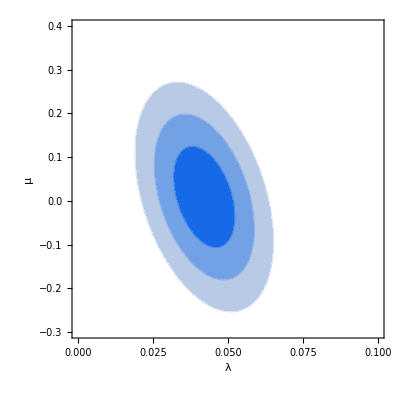

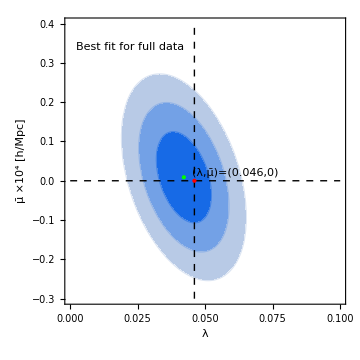

```mathematica
(* λ-μ Contour Plot for  Data *)

contour1=ContourPlot[chi2[data,λ,μ],{λ,0,0.1},{μ,-0.3,0.4},FrameLabel->{"λ","μ"},Contours->{chi2min[[1]]+dchi[1,2],chi2min[[1]]+dchi[2,2],chi2min[[1]]+dchi[3,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White}]

cont=Show[contour1,Graphics[{Inset["Best fit for full data",{0.022,0.34},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["(λ,μ̄)=(0.046,0)",{0.061,0.02},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameLabel->{"λ","μ̄ ×10^4 [h/Mpc]"},PlotRange->{{0,0.1},{-0.3,0.4}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",14},Epilog->{{Dashed,Line[{{0.046,-0.3},{0.046,0.4}}]},{Dashed,Line[{{0,0},{0.1,0}}]},{PointSize[Large],Red,Point[{0.046,0}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

## Figure 2

### Error List Plot from Data

0.042

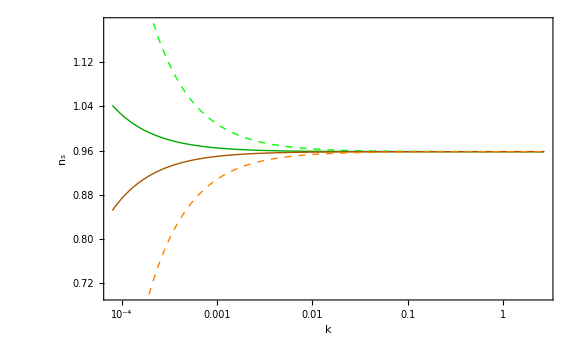

```mathematica
datatab=Table[{data[[i,1]],data[[i,2]],data[[i,3]]},{i,1,Length[data]}];

dataer=ErrorListLogLinearPlot[datatab,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,RGBColor[0.7,0.7,0.9]},ImageSize->Large];
λ=0.042
nsk1[k_,λ_,μ_]:=1-λ - μ/k

plotnsk=LogLinearPlot[Evaluate[Table[nsk1[k,λ,μ],{μ,{-50 10^(-6),-6.7 10^(-6),8.5 10^(-6),50 10^(-6)}}]],{k,0.00008,2.7},Frame->True,FrameLabel->{"k","n_s"},BaseStyle->FontSize->18,PlotStyle->{{PointSize->Large,Dashed,Thick,Green},{PointSize->Large,Thick,Darker[Green]},{PointSize->Large,Thick,Darker[Orange]},{PointSize->Large,Dashed,Thick,Orange}},PlotRange->{0.70,1.19},ImageSize->Large]
```

### HUP - GUP Best Fit on dataset and 1 σ deviation

{{0.000086,0.94979},{0.00010667,0.94649},{0.00012473,0.94772},{0.00014549,0.94841},{0.00016969,0.9491},{0.00019793,0.95116},{0.00023085,0.95116},{0.00026926,0.95116},{0.00031406,0.95254},{0.00036631,0.95391},{0.00042725,0.95391},{0.00049833,0.95391},{0.00058124,0.95506},{0.00067796,0.95666},{0.00079074,0.95666},{0.00092228,0.95689},{0.0010757,0.95804},{0.0012547,0.95804},{0.0014634,0.95804},{0.0017069,0.95804},{0.0019655,0.95873},{0.0023221,0.96079},{0.0027084,0.96079},{0.003159,0.96079},{0.0036845,0.96079},{0.0042974,0.96079},{0.0050123,0.96079},{0.0058461,0.96079},{0.0068186,0.96079},{0.0079529,0.96102},{0.0092762,0.96216},{0.010819,0.96216},{0.012619,0.96125},{0.014718,0.96056},{0.017166,0.95941},{0.020021,0.95941},{0.023351,0.95804},{0.027236,0.95781},{0.031765,0.95621},{0.037049,0.95529},{0.043212,0.95529},{0.0504,0.95529},{0.058785,0.95529},{0.068564,0.95529},{0.079969,0.95529},{0.093273,0.95529},{0.10879,0.95529},{0.12688,0.95483},{0.14799,0.95391},{0.17261,0.95391},{0.20132,0.95391},{0.23481,0.95391},{0.27387,0.95391},{0.31943,0.95368},{0.37256,0.95231},{0.43453,0.95116},{0.50681,0.95116},{0.59112,0.95093},{0.68942,0.9491},{0.8041,0.94841},{0.93785,0.94772},{1.0938,0.94589},{1.2758,0.9452},{1.3955,0.94429},{1.7354,0.94108},{2.024,0.94016},{2.3606,0.93855},{2.6156,0.9381}}

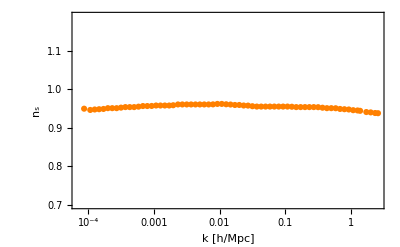

9.×10^-7

0.042

| Estimate | Standard Error | t-Statistic | P-Value
λ | 0.0452582 | 0.000763693 | 59.2623 | 5.87733×10^-59
μ | 6.24657×10^-7 | 2.91823×10^-7 | 2.14053 | 0.0360111

AdjustedRSquared | 0.999965
AIC | -506.43
BIC | -499.771
RSquared | 0.999966

| Estimate | Standard Error | t-Statistic | P-Value
λ | 0.0459675 | 0.000706215 | 65.0899 | 2.69401×10^-62

AdjustedRSquared | 0.999963
AIC | -503.866
BIC | -499.427
RSquared | 0.999963

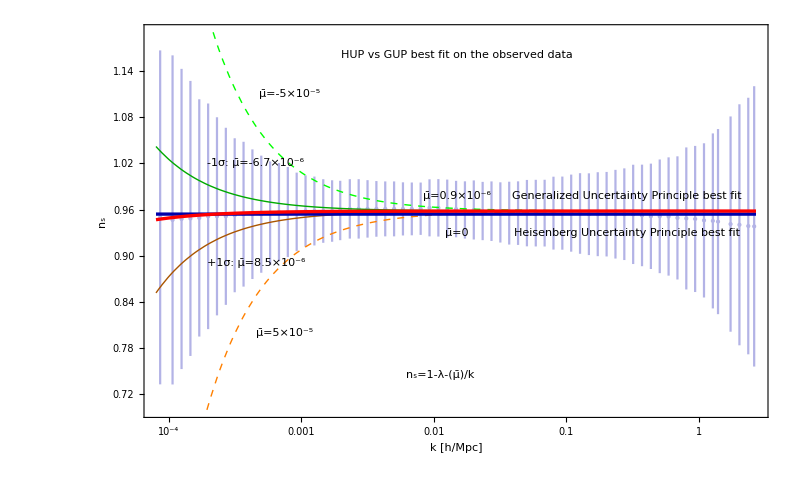

```mathematica
Clear[λ]

dat={{0.000086,0.94979},{0.00010667,0.94649},{0.00012473,0.94772},{0.00014549,0.94841},{0.00016969,0.9491},{0.00019793,0.95116},{0.00023085,0.95116},{0.00026926,0.95116},{0.00031406,0.95254},{0.00036631,0.95391},{0.00042725,0.95391},{0.00049833,0.95391},{0.00058124,0.95506},{0.00067796,0.95666},{0.00079074,0.95666},{0.00092228,0.95689},{0.0010757,0.95804},{0.0012547,0.95804},{0.0014634,0.95804},{0.0017069,0.95804},{0.0019655,0.95873},{0.0023221,0.96079},{0.0027084,0.96079},{0.003159,0.96079},{0.0036845,0.96079},{0.0042974,0.96079},{0.0050123,0.96079},{0.0058461,0.96079},{0.0068186,0.96079},{0.0079529,0.96102},{0.0092762,0.96216},{0.010819,0.96216},{0.012619,0.96125},{0.014718,0.96056},{0.017166,0.95941},{0.020021,0.95941},{0.023351,0.95804},{0.027236,0.95781},{0.031765,0.95621},{0.037049,0.95529},{0.043212,0.95529},{0.0504,0.95529},{0.058785,0.95529},{0.068564,0.95529},{0.079969,0.95529},{0.093273,0.95529},{0.10879,0.95529},{0.12688,0.95483},{0.14799,0.95391},{0.17261,0.95391},{0.20132,0.95391},{0.23481,0.95391},{0.27387,0.95391},{0.31943,0.95368},{0.37256,0.95231},{0.43453,0.95116},{0.50681,0.95116},{0.59112,0.95093},{0.68942,0.9491},{0.8041,0.94841},{0.93785,0.94772},{1.0938,0.94589},{1.2758,0.9452},{1.3955,0.94429},{1.7354,0.94108},{2.024,0.94016},{2.3606,0.93855},{2.6156,0.9381}}

plot1=ListLogLinearPlot[dat,Frame-> True, FrameLabel->{"k [h/Mpc]", "n_s"},PlotStyle->Orange, PlotRange->{0.70,1.19},BaseStyle->FontSize->12]
data1b=Table[{dat[[i,1]],dat[[i,2]]},{i,1,Length[dat]}];
data1c=Table[{dat[[i,1]],dat[[i,2]]},{i,1,Length[dat]}];

plot2=ListLogLinearPlot[data1c,PlotStyle->Orange,PlotRange->{0.70,1.19}];

kmin=0.00008;
kmax=2.7;
μf=0.9 10^(-6)
λf=0.042

nsk1[k_,λ_,μ_]:=1-λ - μ/k

nlmf=NonlinearModelFit[data1b,{nsk1[k,λ,μ]},{λ,μ},k];
plnlmf1=LogLinearPlot[nlmf[k],{k,kmin,kmax},PlotStyle->{Thickness[0.003],Red},PlotRange->{0.70,1.19}];
plnlmf3=LogLinearPlot[nsk1[k,λf,μf],{k,kmin,kmax},PlotStyle->{Thickness[0.003],Red},PlotRange->{0.70,1.19}];

nlmf["ParameterTable"]
Grid[Transpose[{#,nlmf[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

kmin=0.00008;
kmax=2.7;

nsk2[λ_]:=1-λ 

nlmf2=NonlinearModelFit[data1b,{nsk2[λ]},{λ},k];
plnlmf2=LogLinearPlot[nlmf2[k],{k,kmin,kmax},PlotStyle->{Thickness[0.003],Darker[Blue]},PlotRange->{0.70,1.19}];

nlmf2["ParameterTable"]
Grid[Transpose[{#,nlmf2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]

figerbf=Show[dataer,plotnsk,plnlmf2,plnlmf3,Graphics[{Inset["HUP vs GUP best fit on the observed data" ,{-4.2,1.16},BaseStyle->{Small,Bold,Italic,FontFamily->"Times",18}]}],Graphics[{Inset["μ̄=0",{-4.2,0.93},BaseStyle->Directive[Bold,Darker[Blue],Italic,FontFamily->"Times",18]]}],Graphics[{Inset["μ̄=0.9×10^-6",{-4.2,0.978},BaseStyle->Directive[Bold,Red,Italic,FontFamily->"Times",18]]}],Graphics[{Inset["  μ̄=-5×10^-5",{-7.12,1.11},BaseStyle->Directive[Bold,Green,Italic,FontFamily->"Times",18]]}],Graphics[{Inset["-1σ: μ̄=-6.7×10^-6",{-7.7,1.02},BaseStyle->Directive[Bold,Darker[Green],Italic,FontFamily->"Times",18]]}],Graphics[{Inset["+1σ: μ̄=8.5×10^-6",{-7.7,0.89},BaseStyle->Directive[Bold,Darker[Orange],Italic,FontFamily->"Times",18]]}],Graphics[{Inset[" μ̄=5×10^-5",{-7.2,0.80},BaseStyle->Directive[Bold,Orange,Italic,FontFamily->"Times",18]]}],Graphics[{Inset["n_s=1-λ-(μ̄)/k ",{-4.5,0.745},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["Heisenberg Uncertainty Principle best fit",{-1.25,0.93},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",14}]}],
Graphics[{Inset["Generalized Uncertainty Principle best fit",{-1.25,0.978},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"k   [h/Mpc]","n_s"},PlotRange->{0.70,1.19},ImageSize->800,BaseStyle->{Large,FontFamily->"Times",18},Axes->None,LabelStyle->Directive[Black,Large],FrameStyle->Directive[Black,Thick]] 
Export[NotebookDirectory[]<>"figerbf.pdf",figerbf,ImageResolution->1000];
```

## Figure 3 b (Middle Panel)

### Dataset of Large Scales

```mathematica
(* Large scales Data*)

data={{0.000086,0.94979,0.21666},{0.00010667,0.94649,0.213525},{0.00012473,0.94772,0.19478},{0.00014549,0.94841,0.17844},{0.00016969,0.9491,0.15394},{0.00019793,0.95116,0.14638},{0.00023085,0.95116,0.12852},{0.00026926,0.95116,0.114895},{0.00031406,0.95254,0.09991},{0.00036631,0.95391,0.093965},{0.00042725,0.95391,0.084105},{0.00049833,0.95391,0.07597},{0.00058124,0.95506,0.067225},{0.00067796,0.95666,0.063705},{0.00079074,0.95666,0.05845},{0.00092228,0.95689,0.05096},{0.0010757,0.95804,0.04626},{0.0012547,0.95804,0.044685},{0.0014634,0.95804,0.04126},{0.0017069,0.95804,0.039885},{0.0019655,0.95873,0.038535},{0.0023221,0.96079,0.038535},{0.0027084,0.96079,0.038535},{0.003159,0.96079,0.037285},{0.0036845,0.96079,0.03612},{0.0042974,0.96079,0.035645},{0.0050123,0.96079,0.035645},{0.0058461,0.96079,0.034475},{0.0068186,0.96079,0.03426},{0.0079529,0.96102,0.03396},{0.0092762,0.96216,0.03702},{0.010819,0.96216,0.037265},{0.012619,0.96125,0.03757},{0.014718,0.96056,0.03662}}
```

{{0.000086,0.94979,0.21666},{0.00010667,0.94649,0.213525},{0.00012473,0.94772,0.19478},{0.00014549,0.94841,0.17844},{0.00016969,0.9491,0.15394},{0.00019793,0.95116,0.14638},{0.00023085,0.95116,0.12852},{0.00026926,0.95116,0.114895},{0.00031406,0.95254,0.09991},{0.00036631,0.95391,0.093965},{0.00042725,0.95391,0.084105},{0.00049833,0.95391,0.07597},{0.00058124,0.95506,0.067225},{0.00067796,0.95666,0.063705},{0.00079074,0.95666,0.05845},{0.00092228,0.95689,0.05096},{0.0010757,0.95804,0.04626},{0.0012547,0.95804,0.044685},{0.0014634,0.95804,0.04126},{0.0017069,0.95804,0.039885},{0.0019655,0.95873,0.038535},{0.0023221,0.96079,0.038535},{0.0027084,0.96079,0.038535},{0.003159,0.96079,0.037285},{0.0036845,0.96079,0.03612},{0.0042974,0.96079,0.035645},{0.0050123,0.96079,0.035645},{0.0058461,0.96079,0.034475},{0.0068186,0.96079,0.03426},{0.0079529,0.96102,0.03396},{0.0092762,0.96216,0.03702},{0.010819,0.96216,0.037265},{0.012619,0.96125,0.03757},{0.014718,0.96056,0.03662}}

### Theoretical Expression

```mathematica
(* Theoretical Expressions*)
Clear[k,λ,μ];

nsth[k_,λ_,μ_]:=1-λ - μ/(10000  k)
```

### Sigma Difference of Terms

```mathematica
(* Sigma Difference of terms*)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

### Covariance Matrix for Data

```mathematica
(* Covariance Matrix for Data *)

Cij=DiagonalMatrix[data[[All,3]]^2];
InvCij=Inverse[Cij];
Cij//MatrixForm;
```

### Correlated χ^2 Term

```mathematica
(* Correlated χ^2 term *)

vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]
```

### Minimization of χ^2 for Data

```mathematica
(* Minimization of χ^2 for data *)

chi2min=FindMinimum[chi2[data,λ,μ],{λ,.0001,.1},{μ,-0.1,0.1}]
```

{0.0204688,{λ→0.039126,μ→0.0215269}}

### δχ^2 and σ Difference from HUP Best Fit

```mathematica
(* δχ^2 and σ difference from HUP best fit *)

chi2[data,0.045,0]-chi2min[[1]];
nsig[chi2[data,0.045,0]-chi2min[[1]],2]
```

0.220264

### 1 σ Standard Deviations

```mathematica
(* Error 1σ *)

λφ=0.039;
μφ=0.00215;
M=2;
par={μ,λ};
vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]

μkl[λφ_,μ_,k_,l_]:=1/2 D[D[chi2[data,λ,μ],par[[k]],par[[l]] ]]; 
μkls=Table[If[k⩽l,μkl[λ,μ,k,l]/.λ->λφ/.μ->μφ,μkl[λ,μ,l,k]/.λ->λφ/.μ->μφ],{k,1,M},{l,1,M}];
sij=Inverse[μkls];
spar=Table[Sqrt[sij[[i,i]]],{i,1,M}];
Print["{1σμ,1σλ}=",spar];
sij
```

{1σμ,1σλ}={0.081415,0.00952328}

{{0.00662841,-0.000388725},{-0.000388725,0.0000906928}}

### Contour Plot from Dataset of Large Scales

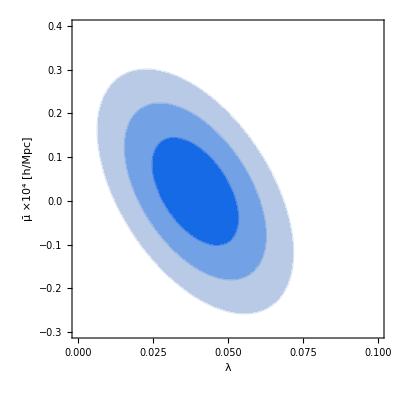

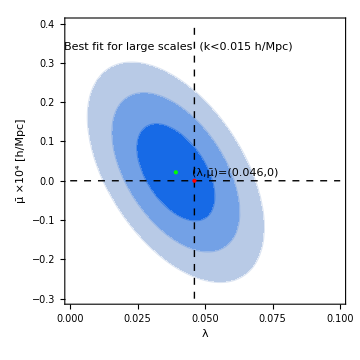

```mathematica
(* λ-μ Contour Plot for  Data *)

contoursmallk=ContourPlot[chi2[data,λ,μ],{λ,0,0.1},{μ,-0.3,0.4},FrameLabel->{"λ","μ̄ ×10^4 [h/Mpc]"},Contours->{chi2min[[1]]+dchi[1,2],chi2min[[1]]+dchi[2,2],chi2min[[1]]+dchi[3,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White}]

contsmallk=Show[contoursmallk,Graphics[{Inset["Best fit for large scales  (k<0.015 h/Mpc)",{0.04,0.34},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["(λ,μ̄)=(0.046,0)",{0.061,0.02},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameLabel->{"λ","μ̄ ×10^4 [h/Mpc]"},PlotRange->{{0,0.1},{-0.3,0.4}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",14},Epilog->{{Dashed,Line[{{0.046,-0.3},{0.046,0.4}}]},{Dashed,Line[{{0,0},{0.1,0}}]},{PointSize[Large],Red,Point[{0.046,0}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

## Figure 3 c (Right Panel)

### Dataset of Small Scales

```mathematica
data={{0.017166,0.95941,0.037135},{0.020021,0.95941,0.038335},{0.023351,0.95804,0.03782},{0.027236,0.95781,0.03864},{0.031765,0.95621,0.03908},{0.037049,0.95529,0.040765},{0.043212,0.95529,0.04126},{0.0504,0.95529,0.04307},{0.058785,0.95529,0.04324},{0.068564,0.95529,0.0433},{0.079969,0.95529,0.047285},{0.093273,0.95529,0.047435},{0.10879,0.95529,0.05001},{0.12688,0.95483,0.052285},{0.14799,0.95391,0.05303},{0.17261,0.95391,0.054455},{0.20132,0.95391,0.054835},{0.23481,0.95391,0.057535},{0.27387,0.95391,0.05947},{0.31943,0.95368,0.064415},{0.37256,0.95231,0.065895},{0.43453,0.95116,0.068355},{0.50681,0.95116,0.07375},{0.59112,0.95093,0.07673},{0.68942,0.9491,0.07991},{0.8041,0.94841,0.092145},{0.93785,0.94772,0.09479},{1.0938,0.94589,0.100045},{1.2758,0.9452,0.11354},{1.3955,0.94429,0.120095},{1.7354,0.94108,0.13967},{2.024,0.94016,0.15637},{2.3606,0.93855,0.16645},{2.6156,0.9381,0.181885}}
```

{{0.017166,0.95941,0.037135},{0.020021,0.95941,0.038335},{0.023351,0.95804,0.03782},{0.027236,0.95781,0.03864},{0.031765,0.95621,0.03908},{0.037049,0.95529,0.040765},{0.043212,0.95529,0.04126},{0.0504,0.95529,0.04307},{0.058785,0.95529,0.04324},{0.068564,0.95529,0.0433},{0.079969,0.95529,0.047285},{0.093273,0.95529,0.047435},{0.10879,0.95529,0.05001},{0.12688,0.95483,0.052285},{0.14799,0.95391,0.05303},{0.17261,0.95391,0.054455},{0.20132,0.95391,0.054835},{0.23481,0.95391,0.057535},{0.27387,0.95391,0.05947},{0.31943,0.95368,0.064415},{0.37256,0.95231,0.065895},{0.43453,0.95116,0.068355},{0.50681,0.95116,0.07375},{0.59112,0.95093,0.07673},{0.68942,0.9491,0.07991},{0.8041,0.94841,0.092145},{0.93785,0.94772,0.09479},{1.0938,0.94589,0.100045},{1.2758,0.9452,0.11354},{1.3955,0.94429,0.120095},{1.7354,0.94108,0.13967},{2.024,0.94016,0.15637},{2.3606,0.93855,0.16645},{2.6156,0.9381,0.181885}}

### Theoretical Expression

```mathematica
(* Theoretical Expressions*)

Clear[k,λ,μ];

nsth[k_,λ_,μ_]:=1-λ - μ/(10000  k)
```

### Sigma Difference of Terms

```mathematica
(* Sigma Difference of terms*)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

### Covariance Matrix for Data

```mathematica
(* Covariance Matrix for Data *)

Cij=DiagonalMatrix[data[[All,3]]^2];
InvCij=Inverse[Cij];
Cij//MatrixForm;
```

### Correlated χ^2 Term

```mathematica
(* Correlated χ^2 term *)

vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]
```

### Minimization of χ^2 for Data

```mathematica
(* Minimization of χ^2 for data *)

chi2min=FindMinimum[chi2[data,λ,μ],{λ,.0001,.1},{μ,-0.1,0.1}]
```

{0.0523534,{λ→0.0481535,μ→-1.49883}}

### δχ^2 and σ Difference from HUP Best Fit

```mathematica
(* δχ^2 and σ difference from HUP best fit *)

chi2[data,0.045,0]-chi2min[[1]];
nsig[chi2[data,0.045,0]-chi2min[[1]],2]
```

0.0480926

### 1 σ Standard Deviations

```mathematica
(* Error 1σ *)

λφ=0.048;
μφ=-1.49;
M=2;
par={μ,λ};
vec[data_,λ_,μ_]:=Table[(data[[i,2]]-nsth[data[[i,1]],λ,μ]),{i,1,Length[data]}];
chi2[data_,λ_,μ_]:=vec[data,λ,μ].InvCij.vec[data,λ,μ]

μkl[λφ_,μ_,k_,l_]:=1/2 D[D[chi2[data,λ,μ],par[[k]],par[[l]] ]]; 
μkls=Table[If[k⩽l,μkl[λ,μ,k,l]/.λ->λφ/.μ->μφ,μkl[λ,μ,l,k]/.λ->λφ/.μ->μφ],{k,1,M},{l,1,M}];
sij=Inverse[μkls];
spar=Table[Sqrt[sij[[i,i]]],{i,1,M}];
Print["{1σμ,1σλ}=",spar];
sij
```

{1σμ,1σλ}={5.35901,0.0146444}

{{28.719,-0.0601895},{-0.0601895,0.000214459}}

### Contour Plot from Dataset of Small Scales

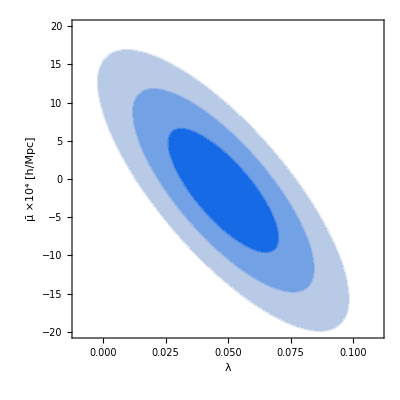

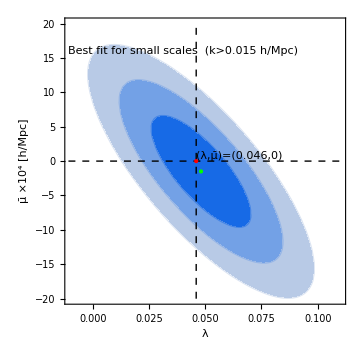

```mathematica
(* λ-μ Contour Plot for  Data *)

contourlargek=ContourPlot[chi2[data,λ,μ],{λ,-0.01,0.11},{μ,-20,20},FrameLabel->{"λ","μ̄ ×10^4 [h/Mpc]"},Contours->{chi2min[[1]]+dchi[1,2],chi2min[[1]]+dchi[2,2],chi2min[[1]]+dchi[3,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.5,.9],Hue[0.6,.2,.9],White}]

contlargek=Show[contourlargek,Graphics[{Inset["Best fit for small scales  (k>0.015 h/Mpc)",{0.04,16},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["(λ,μ̄)=(0.046,0)",{0.065,0.8},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameLabel->{"λ","μ̄ ×10^4 [h/Mpc]"},PlotRange->{{-0.01,0.11},{-20,20}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",14},Epilog->{{Dashed,Line[{{0.046,-20},{0.046,20}}]},{Dashed,Line[{{-0.05,0},{0.15,0}}]},{PointSize[Large],Red,Point[{0.046,0}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

## Figure 3

### Contour Plots from Dataset

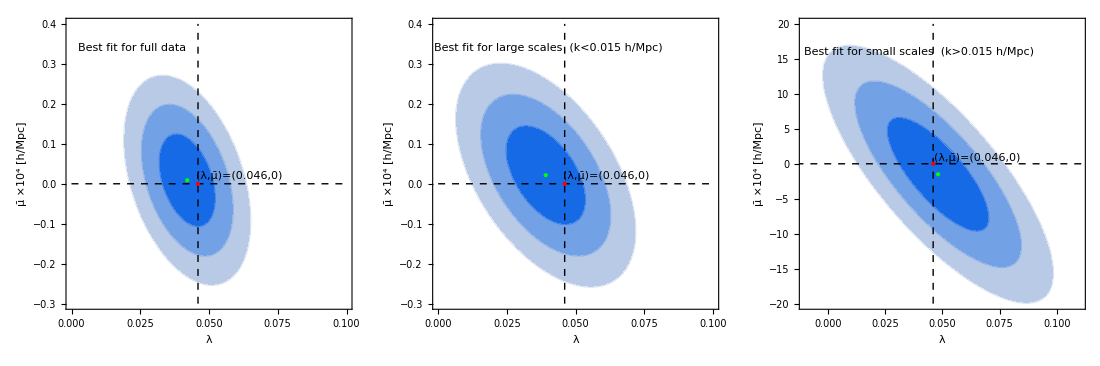

```mathematica
contourfig=GraphicsGrid[{{cont,contsmallk,contlargek}},Spacings->0,ImageSize->1100]
Export[NotebookDirectory[]<>"contourfig.pdf",contourfig,ImageResolution->1000];
```

## Figure 1

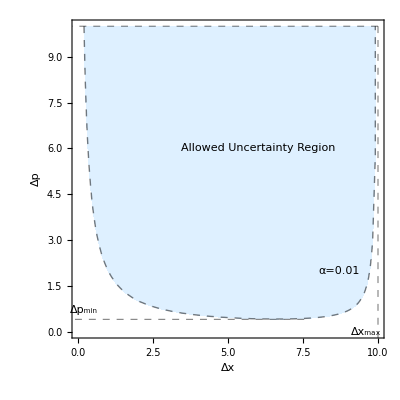

```mathematica
bb=0.0; aa=0.01;ymax=10;xmax=1/Sqrt[aa];
pl1=ContourPlot[ x y-(1/(1-bb  y^2))- (1/(1-aa  x^2)),{x,0.0001,xmax},{y,0.0001,ymax},Contours->{0},ColorFunction->"Pastel",ContourShading->{None,LightBlue},ContourStyle->{Thick,Blue,Dashed}];

gupmaxp=Show[pl1,
Graphics[{Thickness[0.001],Black,Dashed,Line[{{7.538,0.4156},{-0.2212,0.4156}}]}],
Graphics[{Thickness[0.001],Black,Dashed,Line[{{10,10},{10,-0.2212}}]}],
Graphics[{Thickness[0.001],Black,Dashed,Line[{{10,10},{-0.2212,10}}]}],
BaseStyle->{Large,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Large],FrameLabel->{"Δx","Δp"},Epilog->{Text["Allowed Uncertainty Region",{6,6}],Text["Δx_max",{9.6,0.0}],Text["Δp_min",{0.2,0.7}],Text["α=0.01",{8.7,2}]}]
```

```mathematica
Export["gupmax1.pdf",gupmaxp,ImageResolution->1000,ImageSize->Scaled[2]];
```